## 2. noisy LIF

### (a) T_ISI

I have to use “cap” for the capacitance, since Mathematica reserves C for constants of integration or solution.

```mathematica
dvdt=(Subscript[i, app]+(-Subscript[g, L]) (v(t)-Subscript[e, L])+Subscript[i, syn])/cap;
```

```mathematica
soln=Flatten[DSolve[v'(t)==dvdt,v(t),t]]
```

{v[t]→ⅇ^(-(t g_L)/cap) C[1]+(e_L g_L+i_app+i_syn)/g_L}

Find the constant of integration based on v[0]=v_r (using terminology from 4.2.2):

```mathematica
const=Flatten[Solve[(v(t)/.soln/.{t->0})==Subscript[v, r],Subscript[c, 1]]]
```

{C[1]→(-e_L g_L-i_app-i_syn+g_L v_r)/g_L}

Express the result:

```mathematica
voft=Simplify[v(t)/.soln/.const]
```

(e_L g_L+i_app+i_syn-ⅇ^(-(t g_L)/cap) (e_L g_L+i_app+i_syn-g_L v_r))/g_L

Ignoring τ_ref for now, T_ISI will get us from v_r to v_th.
(The assumption and subsequent zeroing for C[1] are only necessary because Mathematica is excessively cautious about letting EVERYTHING be imaginary.)

```mathematica
tsoln=Flatten[Solve[voft==Subscript[v, th],t]];
tsoln=Assuming[Subscript[c, 1]∈Integers,Simplify[tsoln]]/.{Subscript[c, 1]->0}
```

{t→(cap Log[(e_L g_L+i_app+i_syn-g_L v_r)/(e_L g_L+i_app+i_syn-g_L v_th)])/g_L}

Find the steady state

```mathematica
vsssoln=Flatten[Solve[dvdt==0,v(t)]]
```

{v[t]→(e_L g_L+i_app+i_syn)/g_L}

For i_syn=0, this reduces to the form in the text.

Rearrange this into something we can subsittute into T_isi:

```mathematica
replacement=Flatten[Solve[Subscript[v, ss]==(v(t)/.vsssoln),Subscript[i, syn]]];
```

Find T_isi in terms of v_ss (without τ_ref):

```mathematica
Subscript[T, ISINoRef]=Simplify[t/.tsoln/.replacement]
```

(cap Log[(-v_r+v_ss)/(v_ss-v_th)])/g_L

This version has no refractory period. However, since these dynamics occur only after τ_ref has passed, the analysis is piecewise, and we can just add the refractory period:

```mathematica
Subscript[T, ISI]=Subscript[T, ISINoRef]+Subscript[τ, ref]
```

(cap Log[(-v_r+v_ss)/(v_ss-v_th)])/g_L+τ_ref

#### Plot 1/T_ISI vs. I_app

```mathematica
params={Subscript[τ, ref]->0,cap->1,Subscript[g, L]->0.3,Subscript[e, L]->10.6,Subscript[v, r]->0,Subscript[v, th]->30,
Subscript[i, syn]->0(* Subscript[i, syn] could be lumped into Subscript[i, app] .*)
};
tplot=1/Subscript[T, ISI]*1000/.{Subscript[v, ss]->(v[t]/.vsssoln)}/.params
```

300./Log[(3.33333 (3.18+i_app))/(-30+3.33333 (3.18+i_app))]

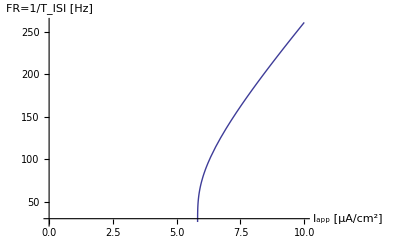

```mathematica
Plot[tplot,{Subscript[i, app],0,10},
AxesLabel->{"I_app  [μA/cm^2]","FR=1/T_ISI  [Hz]"}]
```